```mathematica
ClearAll["Global`*"]
```

```mathematica
proc=ItoProcess[ⅆX[t]==-ⅇ^(-t α) X[t] α Log[X0/K]ⅆt+σ X[t]ⅆW[t],X[t],{X,X0},{t,0},W\[Distributed]WienerProcess[]];
```

```mathematica
Mean[proc[t]]
myF=PDF[proc[t],x]
Integrate[myF/.{t->1,X0->0.1,σ->1,α->1,K->1},{x,0,Infinity}]
```

K (X0/K)^(ⅇ^(-t α))

Piecewise[{{(ⅇ^(-(((t σ^2)/2+Log[x]-Log[X0]+(1-ⅇ^(-t α)) Log[X0/K])^2)/(2 t Abs[σ]^2)))/(√(2 π) √t x Abs[σ]), x>0}, {0, True}}]

1.

```mathematica
FullSimplify[PowerExpand[PDF[proc[t],x]]]
```

Piecewise[{{(ⅇ^(-(((t σ^2)/2-Log[K]+Log[x]+ⅇ^(-t α) (Log[K]-Log[X0]))^2)/(2 t Abs[σ]^2)))/(√(2 π) √t x Abs[σ]), x>0}, {0, True}}]

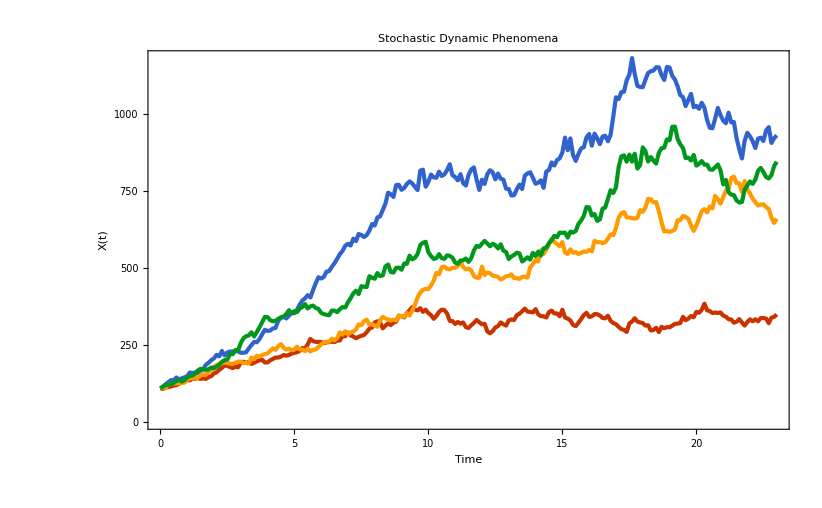

```mathematica
SeedRandom[1004];
data=RandomFunction[proc/.{X0->109.08,σ->0.09,α->0.11,K->1107},{0.,34-11,0.1},4];
ListLinePlot[data,PlotTheme->"Web",PlotRange->All,AxesLabel->{"Time","X(t)"},PlotLabel->"Stochastic Dynamic Phenomena",ImageSize->{822,508},AspectRatio->Full,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Dimensions[Normal[data]]
```

{4,231,2}

```mathematica
Flatten[Normal[data]]
```

{0.,109.08,0.1,107.303,0.2,111.636,0.3,113.387,0.4,115.241,0.5,118.149,0.6,119.567,0.7,124.29,0.8,130.264,0.9,131.255,1.,135.47,1.1,135.064,1.2,141.088,1.3,140.688,1.4,142.282,1.5,139.848,1.6,141.568,1.7,139.86,1.8,145.806,1.9,148.869,2.,157.439,2.1,161.307,2.2,169.364,2.3,175.906,2.4,182.962,2.5,182.569,2.6,177.977,2.7,174.968,2.8,179.16,2.9,177.359,3.,191.675,3.1,195.554,3.2,192.117,3.3,194.586,3.4,188.476,3.5,192.23,3.6,196.782,3.7,199.967,3.8,202.197,3.9,193.195,4.,193.295,4.1,200.203,4.2,204.387,4.3,209.271,4.4,208.947,4.5,212.049,4.6,217.2,4.7,215.326,4.8,217.444,4.9,222.057,5.,224.442,5.1,226.086,5.2,230.948,5.3,240.05,5.4,238.162,5.5,251.76,5.6,269.465,5.7,262.079,5.8,260.164,5.9,259.625,6.,259.364,6.1,256.302,6.2,258.263,6.3,259.157,6.4,260.71,6.5,259.249,6.6,264.046,6.7,264.613,6.8,279.062,6.9,278.373,7.,290.013,7.1,280.875,7.2,277.494,7.3,271.915,7.4,276.351,7.5,279.531,7.6,282.422,7.7,291.276,7.8,302.909,7.9,306.655,8.,323.148,8.1,326.587,8.2,323.18,8.3,303.848,8.4,312.545,8.5,320.383,8.6,314.369,8.7,322.778,8.8,325.386,8.9,345.047,9.,343.186,9.1,339.628,9.2,353.018,9.3,362.289,9.4,372.641,9.5,364.975,9.6,362.29,9.7,369.31,9.8,357.293,9.9,364.383,10.,353.437,10.1,346.849,10.2,334.785,10.3,344.332,10.4,357.349,10.5,364.632,10.6,363.138,10.7,351.992,10.8,328.054,10.9,327.514,11.,318.05,11.1,324.638,11.2,319.167,11.3,322.871,11.4,307.844,11.5,304.959,11.6,314.003,11.7,321.517,11.8,331.035,11.9,323.703,12.,317.024,12.1,318.743,12.2,294.084,12.3,287.655,12.4,295.014,12.5,306.845,12.6,311.032,12.7,322.98,12.8,317.126,12.9,312.811,13.,329.496,13.1,332.744,13.2,330.94,13.3,346.566,13.4,351.441,13.5,359.165,13.6,367.995,13.7,358.389,13.8,357.135,13.9,355.499,14.,366.334,14.1,349.197,14.2,343.496,14.3,342.988,14.4,339.086,14.5,356.668,14.6,361.408,14.7,352.206,14.8,352.367,14.9,343.08,15.,364.234,15.1,339.,15.2,335.566,15.3,329.417,15.4,314.892,15.5,311.055,15.6,321.663,15.7,333.704,15.8,347.344,15.9,354.02,16.,340.991,16.1,342.932,16.2,350.101,16.3,349.857,16.4,345.633,16.5,337.514,16.6,336.501,16.7,344.881,16.8,328.148,16.9,320.959,17.,317.318,17.1,308.514,17.2,301.467,17.3,298.758,17.4,292.057,17.5,319.778,17.6,325.929,17.7,336.72,17.8,325.637,17.9,323.225,18.,320.731,18.1,312.777,18.2,314.108,18.3,296.87,18.4,298.677,18.5,305.59,18.6,291.73,18.7,308.586,18.8,304.343,18.9,307.764,19.,307.306,19.1,312.68,19.2,318.713,19.3,319.234,19.4,321.072,19.5,341.11,19.6,330.294,19.7,335.496,19.8,343.97,19.9,339.984,20.,357.402,20.1,354.459,20.2,364.1,20.3,383.957,20.4,362.61,20.5,359.988,20.6,353.744,20.7,355.238,20.8,353.667,20.9,355.398,21.,345.18,21.1,341.834,21.2,333.542,21.3,332.701,21.4,322.305,21.5,325.484,21.6,333.767,21.7,323.259,21.8,312.852,21.9,324.454,22.,332.99,22.1,326.692,22.2,333.418,22.3,326.857,22.4,337.016,22.5,337.26,22.6,335.729,22.7,320.684,22.8,338.543,22.9,341.085,23.,348.963,0.,109.08,0.1,114.924,0.2,122.357,0.3,129.133,0.4,135.772,0.5,135.836,0.6,144.209,0.7,138.362,0.8,141.752,0.9,144.86,1.,148.157,1.1,160.378,1.2,158.754,1.3,160.877,1.4,158.31,1.5,166.63,1.6,170.291,1.7,185.524,1.8,192.069,1.9,200.688,2.,206.378,2.1,217.854,2.2,213.034,2.3,230.481,2.4,215.898,2.5,225.502,2.6,228.581,2.7,228.683,2.8,230.588,2.9,229.242,3.,224.665,3.1,224.594,3.2,226.152,3.3,238.438,3.4,249.764,3.5,259.701,3.6,258.783,3.7,268.951,3.8,284.624,3.9,298.995,4.,295.5,4.1,296.633,4.2,303.598,4.3,305.086,4.4,328.777,4.5,337.815,4.6,341.276,4.7,336.04,4.8,344.714,4.9,356.483,5.,352.695,5.1,363.757,5.2,380.883,5.3,394.398,5.4,401.1,5.5,411.628,5.6,403.958,5.7,428.538,5.8,450.392,5.9,469.788,6.,465.828,6.1,470.578,6.2,487.756,6.3,489.815,6.4,503.594,6.5,515.354,6.6,529.806,6.7,544.823,6.8,555.265,6.9,571.984,7.,578.246,7.1,572.554,7.2,594.725,7.3,586.913,7.4,610.107,7.5,606.917,7.6,600.202,7.7,606.581,7.8,620.845,7.9,642.379,8.,637.599,8.1,663.986,8.2,667.389,8.3,687.616,8.4,708.834,8.5,744.247,8.6,739.02,8.7,730.511,8.8,768.968,8.9,769.705,9.,753.402,9.1,759.402,9.2,772.638,9.3,780.74,9.4,774.127,9.5,762.89,9.6,752.747,9.7,815.67,9.8,818.791,9.9,763.693,10.,778.53,10.1,802.932,10.2,793.884,10.3,792.683,10.4,812.506,10.5,798.329,10.6,803.787,10.7,817.403,10.8,836.66,10.9,801.064,11.,795.105,11.1,784.226,11.2,804.485,11.3,774.853,11.4,767.229,11.5,801.833,11.6,819.65,11.7,826.326,11.8,786.776,11.9,753.105,12.,786.308,12.1,772.565,12.2,804.024,12.3,816.982,12.4,810.583,12.5,787.452,12.6,806.158,12.7,789.298,12.8,786.701,12.9,757.066,13.,756.094,13.1,735.116,13.2,736.324,13.3,755.257,13.4,770.355,13.5,756.209,13.6,799.535,13.7,806.462,13.8,810.543,13.9,792.626,14.,773.208,14.1,776.833,14.2,784.364,14.3,759.823,14.4,812.388,14.5,817.697,14.6,842.233,14.7,832.147,14.8,849.84,14.9,855.672,15.,874.607,15.1,922.951,15.2,882.005,15.3,920.235,15.4,866.187,15.5,847.392,15.6,869.772,15.7,887.754,15.8,891.52,15.9,923.529,16.,934.767,16.1,896.661,16.2,935.706,16.3,920.398,16.4,901.684,16.5,926.127,16.6,928.915,16.7,911.051,16.8,932.223,16.9,992.016,17.,1053.74,17.1,1048.24,17.2,1070.24,17.3,1071.87,17.4,1109.1,17.5,1127.74,17.6,1181.01,17.7,1128.9,17.8,1090.83,17.9,1087.29,18.,1086.5,18.1,1110.72,18.2,1132.79,18.3,1138.22,18.4,1140.61,18.5,1151.24,18.6,1150.93,18.7,1125.93,18.8,1110.06,18.9,1152.05,19.,1150.37,19.1,1123.16,19.2,1111.33,19.3,1089.46,19.4,1060.72,19.5,1054.27,19.6,1025.31,19.7,1045.46,19.8,1064.72,19.9,1021.4,20.,1025.69,20.1,1016.3,20.2,1035.87,20.3,1019.36,20.4,980.053,20.5,954.667,20.6,953.534,20.7,984.169,20.8,1019.32,20.9,996.087,21.,978.375,21.1,969.564,21.2,1003.85,21.3,972.483,21.4,973.413,21.5,921.311,21.6,885.013,21.7,855.167,21.8,912.744,21.9,938.363,22.,927.248,22.1,911.33,22.2,889.155,22.3,919.642,22.4,922.853,22.5,912.089,22.6,945.896,22.7,956.851,22.8,905.576,22.9,921.003,23.,930.205,0.,109.08,0.1,110.095,0.2,111.697,0.3,120.55,0.4,123.433,0.5,124.969,0.6,124.744,0.7,125.652,0.8,126.322,0.9,127.42,1.,136.302,1.1,141.4,1.2,142.398,1.3,144.367,1.4,142.886,1.5,151.313,1.6,154.517,1.7,153.578,1.8,162.305,1.9,167.951,2.,179.53,2.1,183.766,2.2,189.387,2.3,189.679,2.4,193.462,2.5,191.189,2.6,189.902,2.7,188.359,2.8,192.149,2.9,195.807,3.,195.652,3.1,191.835,3.2,191.201,3.3,189.617,3.4,208.887,3.5,203.162,3.6,215.177,3.7,211.992,3.8,217.357,3.9,220.424,4.,222.638,4.1,230.838,4.2,239.265,4.3,234.2,4.4,245.679,4.5,252.87,4.6,240.846,4.7,235.105,4.8,237.804,4.9,232.92,5.,234.887,5.1,244.521,5.2,235.92,5.3,234.633,5.4,229.746,5.5,237.929,5.6,228.789,5.7,234.184,5.8,235.061,5.9,243.616,6.,251.197,6.1,258.577,6.2,260.032,6.3,260.442,6.4,270.252,6.5,264.765,6.6,271.962,6.7,290.605,6.8,283.668,6.9,294.312,7.,284.48,7.1,290.739,7.2,293.456,7.3,300.017,7.4,316.721,7.5,313.925,7.6,327.645,7.7,331.784,7.8,315.933,7.9,317.568,8.,312.735,8.1,309.379,8.2,329.345,8.3,341.295,8.4,335.944,8.5,332.733,8.6,329.853,8.7,332.041,8.8,329.235,8.9,344.599,9.,343.275,9.1,341.621,9.2,353.521,9.3,345.421,9.4,361.878,9.5,380.56,9.6,404.711,9.7,420.499,9.8,428.942,9.9,432.038,10.,431.433,10.1,442.871,10.2,458.7,10.3,483.781,10.4,479.568,10.5,501.792,10.6,504.306,10.7,496.708,10.8,495.488,10.9,500.197,11.,500.197,11.1,506.274,11.2,521.372,11.3,502.509,11.4,495.447,11.5,497.43,11.6,491.788,11.7,473.385,11.8,468.336,11.9,467.884,12.,504.289,12.1,477.078,12.2,485.43,12.3,482.964,12.4,475.098,12.5,473.437,12.6,470.962,12.7,461.941,12.8,466.961,12.9,472.998,13.,473.908,13.1,479.127,13.2,466.692,13.3,466.686,13.4,464.432,13.5,471.147,13.6,471.732,13.7,468.684,13.8,501.656,13.9,512.207,14.,525.632,14.1,520.947,14.2,557.117,14.3,545.355,14.4,559.724,14.5,576.647,14.6,594.244,14.7,584.192,14.8,577.53,14.9,569.976,15.,583.759,15.1,549.905,15.2,545.295,15.3,560.447,15.4,549.274,15.5,551.255,15.6,545.119,15.7,549.027,15.8,553.169,15.9,552.133,16.,558.521,16.1,553.387,16.2,588.039,16.3,583.4,16.4,583.278,16.5,580.072,16.6,583.7,16.7,594.899,16.8,608.9,16.9,606.233,17.,630.318,17.1,663.082,17.2,677.128,17.3,681.172,17.4,664.047,17.5,663.704,17.6,661.512,17.7,660.001,17.8,662.462,17.9,687.503,18.,681.853,18.1,696.097,18.2,723.997,18.3,722.883,18.4,712.954,18.5,713.69,18.6,683.801,18.7,648.664,18.8,618.529,18.9,619.726,19.,616.98,19.1,620.379,19.2,624.727,19.3,654.798,19.4,654.914,19.5,668.566,19.6,665.732,19.7,659.508,19.8,637.682,19.9,620.267,20.,637.584,20.1,660.871,20.2,684.487,20.3,690.904,20.4,680.201,20.5,699.384,20.6,693.296,20.7,733.65,20.8,722.866,20.9,708.705,21.,729.07,21.1,750.394,21.2,755.679,21.3,791.924,21.4,796.167,21.5,775.255,21.6,774.595,21.7,747.103,21.8,781.898,21.9,754.354,22.,742.129,22.1,724.385,22.2,713.798,22.3,702.462,22.4,705.963,22.5,706.452,22.6,697.296,22.7,691.392,22.8,663.375,22.9,646.05,23.,660.121,0.,109.08,0.1,114.36,0.2,120.136,0.3,120.383,0.4,123.509,0.5,126.68,0.6,133.113,0.7,136.296,0.8,131.12,0.9,135.613,1.,143.754,1.1,149.621,1.2,150.827,1.3,156.52,1.4,167.352,1.5,172.557,1.6,171.735,1.7,169.17,1.8,170.776,1.9,176.626,2.,173.997,2.1,179.716,2.2,185.585,2.3,195.402,2.4,200.668,2.5,202.615,2.6,220.637,2.7,219.819,2.8,233.426,2.9,231.33,3.,255.978,3.1,271.591,3.2,278.237,3.3,280.851,3.4,291.053,3.5,277.385,3.6,291.821,3.7,306.997,3.8,323.643,3.9,340.902,4.,340.426,4.1,330.62,4.2,326.75,4.3,328.567,4.4,334.7,4.5,340.021,4.6,342.056,4.7,349.902,4.8,362.903,4.9,351.477,5.,359.724,5.1,356.381,5.2,368.195,5.3,373.032,5.4,382.646,5.5,368.342,5.6,375.283,5.7,377.611,5.8,370.037,5.9,367.188,6.,354.15,6.1,350.101,6.2,347.841,6.3,346.5,6.4,361.661,6.5,361.174,6.6,356.549,6.7,366.126,6.8,372.909,6.9,371.589,7.,388.404,7.1,401.647,7.2,417.238,7.3,425.87,7.4,414.904,7.5,440.667,7.6,438.858,7.7,437.932,7.8,473.06,7.9,468.213,8.,464.985,8.1,483.48,8.2,473.424,8.3,475.822,8.4,504.765,8.5,511.047,8.6,486.465,8.7,484.972,8.8,500.187,8.9,500.762,9.,494.108,9.1,514.053,9.2,513.333,9.3,539.777,9.4,527.918,9.5,532.89,9.6,545.446,9.7,574.499,9.8,581.706,9.9,584.755,10.,551.264,10.1,538.668,10.2,529.19,10.3,531.793,10.4,544.747,10.5,531.698,10.6,529.279,10.7,540.812,10.8,539.078,10.9,533.21,11.,517.379,11.1,513.384,11.2,524.133,11.3,524.787,11.4,530.422,11.5,519.435,11.6,532.107,11.7,556.304,11.8,571.447,11.9,568.363,12.,578.638,12.1,587.585,12.2,579.228,12.3,570.345,12.4,578.245,12.5,573.648,12.6,563.255,12.7,576.63,12.8,555.766,12.9,551.974,13.,528.805,13.1,537.26,13.2,541.976,13.3,549.46,13.4,546.922,13.5,520.952,13.6,527.041,13.7,534.338,13.8,526.985,13.9,548.515,14.,538.772,14.1,552.975,14.2,540.274,14.3,563.363,14.4,565.525,14.5,580.596,14.6,590.499,14.7,604.036,14.8,599.421,14.9,614.615,15.,613.614,15.1,614.495,15.2,598.568,15.3,617.658,15.4,614.727,15.5,619.882,15.6,642.733,15.7,653.804,15.8,668.857,15.9,697.725,16.,696.455,16.1,670.044,16.2,674.904,16.3,652.626,16.4,657.43,16.5,692.41,16.6,696.146,16.7,724.191,16.8,752.059,16.9,742.974,17.,762.045,17.1,827.026,17.2,862.069,17.3,865.363,17.4,844.844,17.5,867.546,17.6,845.108,17.7,870.593,17.8,822.354,17.9,833.252,18.,891.087,18.1,878.605,18.2,845.221,18.3,859.875,18.4,847.871,18.5,838.518,18.6,873.491,18.7,888.288,18.8,890.216,18.9,917.218,19.,914.4,19.1,958.084,19.2,958.515,19.3,918.53,19.4,901.099,19.5,889.288,19.6,856.28,19.7,857.935,19.8,848.669,19.9,866.816,20.,832.014,20.1,837.583,20.2,846.73,20.3,835.33,20.4,835.079,20.5,819.544,20.6,818.426,20.7,826.359,20.8,835.738,20.9,817.136,21.,771.31,21.1,785.508,21.2,746.121,21.3,737.757,21.4,736.353,21.5,718.989,21.6,712.189,21.7,713.642,21.8,753.975,21.9,767.033,22.,780.527,22.1,772.519,22.2,786.794,22.3,814.793,22.4,824.478,22.5,811.427,22.6,795.17,22.7,790.34,22.8,801.315,22.9,830.468,23.,844.751}

```mathematica
Export["sdedata4.csv",Flatten[Normal[data]]]
```

sdedata4.csv

```mathematica
data
```

TemporalData[…]

```mathematica
Normal[%1450]
```

{{{0.,2.},{0.01,2.03729},{0.02,2.01978},{0.03,2.03558},{0.04,2.00681},{0.05,1.98563},{0.06,1.94941},{0.07,1.96417},{0.08,1.97929},{0.09,1.95536},{0.1,1.97823},{0.11,1.95992},{0.12,1.96688},{0.13,1.988},{0.14,2.00368},{0.15,2.01036},{0.16,1.97192},{0.17,1.9871},{0.18,1.99156},{0.19,1.95651},{0.2,1.9985},{0.21,1.98973},{0.22,2.00669},{0.23,2.00791},{0.24,1.99114},{0.25,1.99994},{0.26,1.9775},{0.27,1.96161},{0.28,1.92826},{0.29,1.90973},{0.3,1.88766},{0.31,1.86354},{0.32,1.83859},{0.33,1.83251},{0.34,1.85847},{0.35,1.83737},{0.36,1.83047},{0.37,1.83475},{0.38,1.85086},{0.39,1.82684},{0.4,1.83395},{0.41,1.83485},{0.42,1.87111},{0.43,1.87564},{0.44,1.90507},{0.45,1.93706},{0.46,1.89148},{0.47,1.89394},{0.48,1.90425},{0.49,1.91173},{0.5,1.90078},{0.51,1.91644},{0.52,1.92237},{0.53,1.91725},{0.54,1.89627},{0.55,1.89771},{0.56,1.90802},{0.57,1.90019},{0.58,1.90342},{0.59,1.9068},{0.6,1.865},{0.61,1.87404},{0.62,1.87687},{0.63,1.9184},{0.64,1.91845},{0.65,1.94251},{0.66,1.94002},{0.67,1.94159},{0.68,1.95109},{0.69,1.96922},{0.7,1.99396},{0.71,1.94933},{0.72,1.96791},{0.73,1.98186},{0.74,1.98529},{0.75,1.98646},{0.76,2.01373},{0.77,2.02348},{0.78,2.002},{0.79,2.02887},{0.8,2.02997},{0.81,2.01677},{0.82,2.02889},{0.83,2.06048},{0.84,2.0361},{0.85,2.00044},{0.86,2.00271},{0.87,2.01775},{0.88,1.99678},{0.89,1.98848},{0.9,2.01812},{0.91,2.05574},{0.92,2.06356},{0.93,2.06357},{0.94,2.05037},{0.95,2.04347},{0.96,2.05072},{0.97,2.04417},{0.98,2.03008},{0.99,2.00626},{1.,2.00224}}}

```mathematica
Flatten[%1451]
```

{0.,2.,0.01,2.03729,0.02,2.01978,0.03,2.03558,0.04,2.00681,0.05,1.98563,0.06,1.94941,0.07,1.96417,0.08,1.97929,0.09,1.95536,0.1,1.97823,0.11,1.95992,0.12,1.96688,0.13,1.988,0.14,2.00368,0.15,2.01036,0.16,1.97192,0.17,1.9871,0.18,1.99156,0.19,1.95651,0.2,1.9985,0.21,1.98973,0.22,2.00669,0.23,2.00791,0.24,1.99114,0.25,1.99994,0.26,1.9775,0.27,1.96161,0.28,1.92826,0.29,1.90973,0.3,1.88766,0.31,1.86354,0.32,1.83859,0.33,1.83251,0.34,1.85847,0.35,1.83737,0.36,1.83047,0.37,1.83475,0.38,1.85086,0.39,1.82684,0.4,1.83395,0.41,1.83485,0.42,1.87111,0.43,1.87564,0.44,1.90507,0.45,1.93706,0.46,1.89148,0.47,1.89394,0.48,1.90425,0.49,1.91173,0.5,1.90078,0.51,1.91644,0.52,1.92237,0.53,1.91725,0.54,1.89627,0.55,1.89771,0.56,1.90802,0.57,1.90019,0.58,1.90342,0.59,1.9068,0.6,1.865,0.61,1.87404,0.62,1.87687,0.63,1.9184,0.64,1.91845,0.65,1.94251,0.66,1.94002,0.67,1.94159,0.68,1.95109,0.69,1.96922,0.7,1.99396,0.71,1.94933,0.72,1.96791,0.73,1.98186,0.74,1.98529,0.75,1.98646,0.76,2.01373,0.77,2.02348,0.78,2.002,0.79,2.02887,0.8,2.02997,0.81,2.01677,0.82,2.02889,0.83,2.06048,0.84,2.0361,0.85,2.00044,0.86,2.00271,0.87,2.01775,0.88,1.99678,0.89,1.98848,0.9,2.01812,0.91,2.05574,0.92,2.06356,0.93,2.06357,0.94,2.05037,0.95,2.04347,0.96,2.05072,0.97,2.04417,0.98,2.03008,0.99,2.00626,1.,2.00224}

```mathematica
ExportString[-ⅇ^(-t α) X[t] α Log[X0/K]ⅆt+σ X[t]ⅆW[t],"TeX"]
```

%% AMS-LaTeX Created with the Wolfram Language : www.wolfram.com\r
\r
\documentclass{article}\r
\usepackage{amsmath, amssymb, graphics, setspace}\r
\r
\newcommand{\mathsym}[1]{{}}\r
\newcommand{\unicode}[1]{{}}\r
\r
\newcounter{mathematicapage}\r
\begin{document}\r
\r
\[\sigma  dW[t] X[t]-e^{-t \alpha } \alpha  dt \text{Log}\left[\frac{\text{X0}}{K}\right] X[t]\]\r
\r
\end{document}\r